```mathematica
Import["/home/syang/Downloads/MG5_aMC_v2_6_5/EventTools.m"]
```

```mathematica
data=Get["/home/syang/Downloads/MG5_aMC_v2_6_5/pptt/Events/run_01/output"]
```

{{{6,-23.9832,1.0384,-209.308,272.608},{-6,23.9832,-1.0384,-7.24287,174.808}},9998,{{6,-102.65,21.295,-301.023,362.677},{-6,102.65,-21.295,-332.316,389.042}}}
 |  |  |  |

```mathematica
data//Length
```

10000

```mathematica
data[[All,1]][[All,2;;5]]
```

{{-23.9832,1.0384,-209.308},{-20.4225,25.2414,-200.878},{-110.179,-61.9979,4.57923},9995,{123.155,129.933,136.793},{-102.65,21.295,-301.023}}
 |  |  |  |

```mathematica
hisData=pT/@data[[All,1]][[All,2;;5]];
```

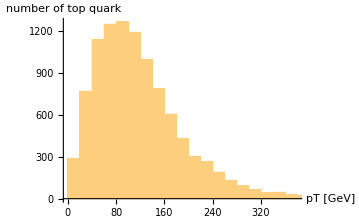

```mathematica
Histogram[hisData,50,AxesLabel->{"pT [GeV]", "number of top quark"}]
```

```mathematica
Mean[hisData]
```

119.798